```mathematica
img = -Graphics-;
```

```mathematica
RangeMakeAround[num_Integer, delta_Integer] := Range[num - delta, num + delta];
ColorsMakeShade[redVals_List, greenVals_List, blueVals_List] := Tuples[{redVals, greenVals, blueVals, { 255 }}];
ColorsMakeShade[red_Integer, green_Integer, blue_Integer, delta_Integer] := ColorsMakeShade[RangeMakeAround[red, delta],RangeMakeAround[green, delta],RangeMakeAround[blue, delta]];
ColorsMakeShade[grey_Integer, delta_Integer] := ColorsMakeShade[grey, grey, grey, delta];
```

```mathematica
ColorsFindInImage[img_, colors_List] := Flatten[Join[Map[(Position[img, #]) &, colors]]];
MapReconstructFromImages[imgs_List] := Module[{cntSide, imgsTable}, 
	cntSide = Sqrt[Length[imgs]];
	imgsTable = ArrayReshape[imgs, {cntSide,cntSide}];
	ImageAssemble[imgsTable]
];
ColorMake[r_,g_,b_] := RGBColor[r/255, g/255, b/255];
ColorMake[parts_List] := ColorMake[parts⟦1⟧, parts⟦2⟧, parts⟦3⟧];
```

```mathematica
colorsPerPurpose = Association[{
	"Street" -> ColorsMakeShade[254, 1], 
	"Highway" -> Join[ColorsMakeShade[232, 208, 174, 1], ColorsMakeShade[227, 160, 54, 1], ColorsMakeShade[242, 196, 99, 1]],
	"Water" -> ColorsMakeShade[158, 197, 226, 1],
	"Park" -> Join[ColorsMakeShade[201, 224, 185, 1], ColorsMakeShade[196, 211, 192, 1](*walking trails*)],
	"Train" -> ColorsMakeShade[148, 1],
	"Interesting" -> Join[ColorsMakeShade[251, 248, 228, 1], ColorsMakeShade[240, 236, 228, 1](*sports*)],
	"Building" -> Join[ColorsMakeShade[232, 226, 212, 3], {(*
			{207,200,188}, {207,202,193}, {224,217,205}, {214,210,204}, {215,210,200}, {226,220,209}, {217,212,202}, 
			{226,223,218}, {235,233,231}, {237,236,233}, {192,186,175}, {202,197,187}, {217,214,208}, {225,221,216}, 
			{231,226,218}, {219,215,210}, {212,208,200}, {230,227,223}, {239,237,234}
		*)}]
}];
```

```mathematica
colorsPerPurpose = Association[{
	"Street" -> {{254,254,254}}, 
	"Highway" -> {{232,208,174}, {227,160,54}, {242,196,99}},
	"Water" -> {{158,197,226}},
	"Park" -> {{201,224,185}, {196,211,192}(*walking trails*)},
	"Train" -> {{148,148,148}},
	"Interesting" -> {{251,248,228}, {240,236,228}(*sports*)},
	"Building" -> {{232,226,212}, {235,233,231}, {192,186,175}, {207,200,188}},
	"Annotations" -> {{69,69,69}, {117,117,117}, {63,63,63}, {88,88,88}}
}];
```

```mathematica
imgClean = RemoveAlphaChannel[ColorQuantize[img, Map[ColorMake, Flatten[Values[colorsPerPurpose], {1, 2}]]]];
imgBytes = Flatten[ImageData[imgClean, "Byte"], 1];
statsAreaShareByPurpose = AssociationMap[(Length[ColorsFindInImage[imgBytes, colorsPerPurpose[#]]] / Length[imgBytes]) &, Keys[colorsPerPurpose]];
```

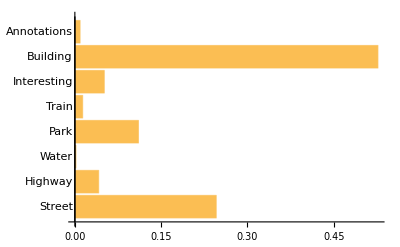

```mathematica
BarChart[Values[statsAreaShareByPurpose],ChartLabels->Keys[statsAreaShareByPurpose],BarOrigin->Left]
```

```mathematica
cityBounds = GeoBoundingBox[GeoPosition[Entity["City",{"NewYork","NewYork","UnitedStates"}]], Quantity[5, "Kilometers"]];
(*cityBounds = GeoDisk[GeoPosition[Entity["City",{"Moscow","Moscow","Russia"}]], Quantity[5, "Kilometers"]];*)
GeoPosition[Entity["City",{"NewYork","NewYork","UnitedStates"}]]
```

GeoPosition[{40.6643,-73.9385}]

```mathematica
cityBounds = GeoBoundingBox[GeoPosition[Entity["City",{"NewYork","NewYork","UnitedStates"}]],Quantity[0.5, "Kilometers"]];
osmData = ResourceFunction["OSMImport"][cityBounds];
osmNodes = Map[Lookup[#, "Position"] &, osmData["Nodes"]];
```

```mathematica
osmWays = Map[Lookup[osmNodes, Lookup[#, "Nodes"]] &, Select[osmData["Ways"], MemberQ[Keys[#Tags],"highway"] &]];
```

```mathematica
roadEdges = Flatten[Map[UndirectedEdge@@@Partition[#,2,1] &, Values[osmWays]]];
```

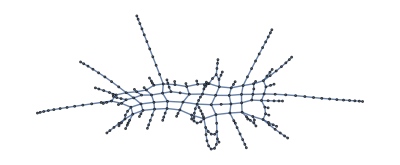

```mathematica
roadsDisconnectedGraph = Graph[roadEdges]
```

```mathematica
connectedComponents=ConnectedGraphComponents[roadsDisconnectedGraph];
Column[{roadsGraph,roadsOrphanedGraphs}=Through[{First,Rest}[connectedComponents]]]
```

-Graphics-
{}

```mathematica
Mean[MeanNeighborDegree[roadsDisconnectedGraph]]
```

2059/790

```mathematica
Mean[DegreeCentrality[roadsDisconnectedGraph]]
```

550/237

```mathematica
Mean[ClosenessCentrality[roadsDisconnectedGraph]]
```

0.096186

```mathematica
LocalClusteringCoefficient[roadsDisconnectedGraph]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}